```mathematica
(* This notebook contains all code used to generate figures for  *)
```

```mathematica
ClearAll["Global`*"]
```

## Always run first: Spin operators and functions

```mathematica
(* Electronic spin operators *)
I2 = IdentityMatrix[2]; Sx =1/2 PauliMatrix[1]; Sy =1/2 PauliMatrix[2]; Sz =1/2 PauliMatrix[3];

(* Nuclear spin operators *)
(* Khadija's code for producing operators of arbitrary spin *)
SpinX[S0_]:=Module[{S=S0},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,el[[i]][[j]]=(1/2)*(KroneckerDelta[mdash[[i]],m[[j]]+1]+KroneckerDelta[mdash[[i]]+1,m[[j]]])Sqrt[S(S+1)-mdash[[i]]m[[j]]]]];el]
SpinY[S0_]:=Module[{S=S0},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,el[[i]][[j]]=(1/2I)*(KroneckerDelta[mdash[[i]],m[[j]]+1]-KroneckerDelta[mdash[[i]]+1,m[[j]]])Sqrt[S(S+1)-mdash[[i]]m[[j]]]]];el]
SpinZ[S0_]:=Module[{S=S0},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,el[[i]][[j]]=KroneckerDelta[mdash[[i]],m[[j]]]m[[j]]]];el];


CircleTimes[A_,B_] := KroneckerProduct[A,B];
Commute[A_,B_] := A.B - B.A;

Iz = SpinZ[3/2];
Ix = SpinX[3/2];
Iy = SpinY[3/2];
I2 = IdentityMatrix[2];
```

## Run these first for corresponding plots: one-tangling power calculations

### Free evolution one-tangling power for single nucleus (Fig. 1(a))

```mathematica
(* free evolution single nuclear one-tangling power for numerical approach *)
(* CPMG nuclear one-tangling power *)
nuclearonetanglefree[ωn1_, a_, Dq_, anc1_, θ1_,tvals_]:= Module[{M1, M2, M1List,  M2List, R0free,R0freedag,  R1free, R1freedag,  G1freept1, G1freept2, TrG1freept1, TrG1freept2, d, G1free}, 

(* Setting up matrices that will form rotation operators *)
M1[t_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[t_]:=(ωn1 Iz -1/2 a Iz +Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t;

(* Generate all possible values over time *)
M1List = ParallelTable[M1[t],{t,tvals}];
M2List = ParallelTable[M2[t],{t,tvals}];

(* Form free evolution rotation operators *)
R0free=Map[MatrixExp[-I*#]&,M1List];
R1free=Map[MatrixExp[-I*#]&,M2List];

R0freedag=Map[MatrixExp[I*#]&,M1List];
R1freedag=Map[MatrixExp[I*#]&,M2List];

(* Build up G1 in parts *)
G1freept1 = MapThread[#1.#2&,{R0free,R1freedag}];
G1freept2 = MapThread[#1.#2&,{R0freedag,R1free}];

TrG1freept1 = Map[Tr,G1freept1];
TrG1freept2 = Map[Tr,G1freept2];

d = 4;
G1free = 1/d^2 TrG1freept1*TrG1freept2;

1/3(d/(d+1))(1 - G1free)//Chop

]
```

### CPMG electronic one-tangling power for 80,000 nuclei (Fig. 3(a))

```mathematica
eop[tvals_]:= Module[{rstart, rend, rstep, rvals, nn, nnvals, hfvalsfunc, avals, qvalsfunc, qvals, avalscount,qvalscount, rcounts,astart,aend,astep, M0,M1,M0list,M1list, R0, R0dag, R1, R1dag, G1pt1,G1pt2, TrG1CPMGpt1,TrG1CPMGpt2, G1free, M1Listtest, M2Listtest, R0freetest, R1freetest, R0freetestdag, R1freetestdag, R0test, R1test, R0testdag, R1testdag, sepprod, NN, R, ρ, M2, d, R0CPMG, R0CPMGdag, R1CPMG, R1CPMGdag, G1CPMGpt1, G1CPMGpt2, ProdsCPMG, G1CPMG},

(* Now use nuclear hf and quadrupolar coupling values from distribution *)
(* First solve for the density of spins per area in the dot *)
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.056;(* dr *)

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;
(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = ParallelTable[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);

avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius-- don't need here *)
(* rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten; *)

M1[i_]:=ωn1 Iz+1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));
M2[i_]:=ωn1 Iz-1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)); 

M1Listtest = ParallelTable[M1[i],{i,Length[avalscount]}];
M2Listtest = ParallelTable[M2[i],{i,Length[avalscount]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t]; 

R0CPMG[t_] := MapThread[#1.#2.#3&,{R0freetest[t/4],R1freetest[t/2],R0freetest[t/4]}];
R0CPMGdag[t_] := MapThread[#1.#2.#3&,{R0freetestdag[t/4],R1freetestdag[t/2],R0freetestdag[t/4]}];

R1CPMG[t_] := MapThread[#1.#2.#3&,{R1freetest[t/4],R0freetest[t/2],R1freetest[t/4]}];
R1CPMGdag[t_] := MapThread[#1.#2.#3&,{R1freetestdag[t/4],R0freetestdag[t/2],R1freetestdag[t/4]}];

G1CPMGpt1[t_] := MapThread[#1.#2&,{R0CPMG[t], R1CPMGdag[t]}];
G1CPMGpt2[t_] := MapThread[#1.#2&,{R0CPMGdag[t], R1CPMG[t]}];

TrG1CPMGpt1[t_]:= Map[Tr,G1CPMGpt1[t]];
TrG1CPMGpt2[t_] := Map[Tr,G1CPMGpt2[t]];

G1CPMG[t_] := 1/16 TrG1CPMGpt1[t]*TrG1CPMGpt2[t];

d = 4;

ProdsCPMG = {};
For[i=1,i<= Length[tvals],i++, AppendTo[ProdsCPMG, Fold[Times,1,(1+ d G1CPMG[tvals[[i]]])]]];

 1/3-1/3(1/(d+1))^Length[avalscount]*ProdsCPMG

]
```

### CPMG electronic one-tangling power for 272 nuclei (Fig. 3(b))

```mathematica
eopCPMGsmall[ωn1_, tvals_]:= Module[{rstart, rend, rstep, rvals, nn, nnvals, hfvalsfunc, avals, qvalsfunc, qvals, avalscount,qvalscount, rcounts,astart,aend,astep, M0,M1,M0list,M1list, R0, R0dag, R1, R1dag, G1pt1,G1pt2, TrG1CPMGpt1,TrG1CPMGpt2, G1free, M1Listtest, M2Listtest, R0freetest, R1freetest, R0freetestdag, R1freetestdag, R0test, R1test, R0testdag, R1testdag, sepprod, NN, R, ρ, M2, d, R0CPMG, R0CPMGdag, R1CPMG, R1CPMGdag, G1CPMGpt1, G1CPMGpt2, ProdsCPMG, G1CPMG},

(* Now use nuclear hf and quadrupolar coupling values from distribution *)
(* First solve for the density of spins per area in the dot *)
NN = 100;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.0918;(* 0.056; *)(* 0.00031250390629882874;*) (* dr *)

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;
(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = ParallelTable[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);

avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius-- don't need here *)
(* rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten; *)

M1[i_]:=ωn1 Iz+1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));
M2[i_]:=ωn1 Iz-1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)); 

M1Listtest = ParallelTable[M1[i],{i,Length[avalscount]}];
M2Listtest = ParallelTable[M2[i],{i,Length[avalscount]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t]; 

R0CPMG[t_] := MapThread[#1.#2.#3&,{R0freetest[t/4],R1freetest[t/2],R0freetest[t/4]}];
R0CPMGdag[t_] := MapThread[#1.#2.#3&,{R0freetestdag[t/4],R1freetestdag[t/2],R0freetestdag[t/4]}];

R1CPMG[t_] := MapThread[#1.#2.#3&,{R1freetest[t/4],R0freetest[t/2],R1freetest[t/4]}];
R1CPMGdag[t_] := MapThread[#1.#2.#3&,{R1freetestdag[t/4],R0freetestdag[t/2],R1freetestdag[t/4]}];

G1CPMGpt1[t_] := MapThread[#1.#2&,{R0CPMG[t], R1CPMGdag[t]}];
G1CPMGpt2[t_] := MapThread[#1.#2&,{R0CPMGdag[t], R1CPMG[t]}];

TrG1CPMGpt1[t_]:= Map[Tr,G1CPMGpt1[t]];
TrG1CPMGpt2[t_] := Map[Tr,G1CPMGpt2[t]];

G1CPMG[t_] := 1/16 TrG1CPMGpt1[t]*TrG1CPMGpt2[t];

d = 4;

ProdsCPMG = {};
For[i=1,i<= Length[tvals],i++, AppendTo[ProdsCPMG, Fold[Times,1,(1+ d G1CPMG[tvals[[i]]])]]];

 1/3-1/3(1/(d+1))^Length[avalscount]*ProdsCPMG

]
```

### CPMG one-tangling power for single nucleus (Fig. 6(a), (b), (c))

```mathematica
(* CPMG nuclear one-tangling power *)
nuclearonetangleCPMG[ωn1_, a_, Dq_, anc1_, θ1_, NN_,tvals_]:= Module[{M1, M2, M1List2, M1List4, M2List2, M2List4, R04, R14, R0dag2, R0dag4, R1dag2, R1dag4, R02, R12, R0CPMG2, R0CPMGdag2, R1CPMG2, R1CPMGdag2, G1CPMGpt12, G1CPMGpt22, TrG1CPMGpt12, TrG1CPMGpt22, d, G1CPMG2}, 

(* Setting up matrices that will form rotation operators *)
M1[t_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[t_]:=(ωn1 Iz -1/2 a Iz +Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t;

(* Generate all possible values over time *)
M1List4 = ParallelTable[M1[t/4],{t,tvals}];
M2List4 = ParallelTable[M2[t/4],{t,tvals}];
M1List2 = ParallelTable[M1[t/2],{t,tvals}];
M2List2 = ParallelTable[M2[t/2],{t,tvals}];

(* Form free evolution rotation operators *)
R04=Map[MatrixExp[-I*#]&,M1List4];
R14=Map[MatrixExp[-I*#]&,M2List4];

R0dag4=Map[MatrixExp[I*#]&,M1List4];
R1dag4=Map[MatrixExp[I*#]&,M2List4];

R02=Map[MatrixExp[-I*#]&,M1List2];
R12=Map[MatrixExp[-I*#]&,M2List2];

R0dag2=Map[MatrixExp[I*#]&,M1List2];
R1dag2=Map[MatrixExp[I*#]&,M2List2];

(* Build CPMG rotation operators out of the above free evolution ones *)
R0CPMG2 = MapThread[MatrixPower[#1.#2.#3,NN]&,{R04,R12,R04}]//Chop;
R0CPMGdag2 = MapThread[MatrixPower[#1.#2.#3,NN]&, {R0dag4,R1dag2,R0dag4}]//Chop;
R1CPMG2 = MapThread[MatrixPower[#1.#2.#3,NN]&, {R14,R02,R14}]//Chop;
R1CPMGdag2 = MapThread[MatrixPower[#1.#2.#3,NN]&,{R1dag4, R0dag2, R1dag4}]//Chop; 

(* Build up G1 in parts *)
G1CPMGpt12 = MapThread[#1.#2&,{R0CPMG2,R1CPMGdag2}];
G1CPMGpt22 = MapThread[#1.#2&,{R0CPMGdag2,R1CPMG2}];

TrG1CPMGpt12 = Map[Tr,G1CPMGpt12];
TrG1CPMGpt22 = Map[Tr,G1CPMGpt22];

d = 4;
G1CPMG2 = 1/d^2 TrG1CPMGpt12*TrG1CPMGpt22;

1/3(d/(d+1))(1 - G1CPMG2)//Chop

]
```

## Fig. 1

### Fig. 1(a)

```mathematica
(* parameters used in MHz where applicable *)
a1 = 0.23*2π;
ωn1 = 12.98*2π;
Dq1 = 2π*0.034;
anc1 = 2π*0.056;

θ1 = π/3;

(* time in μs *)
tstart = 0;
tend = 12;
tstep = 0.01;
tvals = ParallelTable[t,{t,tstart,tend,tstep}];
```

```mathematica
(* resonance times *)
restimes = {};
For[i = 0,i<= 10, i++, AppendTo[restimes, ((2 i + 1)π)/a1]];
For[i = 0,i<= 10, i++, AppendTo[restimes, ((2 i + 1)π)/(2 a1)]];
restimes;
```

```mathematica
(* numerical one-tangling power *)
NOTPvals = nuclearonetanglefree[ωn1, a1, Dq1, anc1, θ1, tvals];
```

```mathematica
(* analytical one-tangling power *)
G1freeanalytical[t_] := 1/2 Cos[a1 t]^2(1 + Cos[a1 t]);
d = 4;
epsilonfreeanalytical[t_] := 1/3(d/(d+1))(1 - G1freeanalytical[t]);

NOTPvalsanalytical = ParallelTable[epsilonfreeanalytical[t],{t,tvals}];
```

```mathematica
(* Fig. 1(a): Free evolution nuclear one-tangling power *)
ListPlot[{Transpose[{tvals,NOTPvals}],Transpose[{tvals,NOTPvalsanalytical}]},Joined-> True, Frame-> True,FrameLabel->{"t (μs)","ϵ^nuclear"}, LabelStyle->{Directive[Black],30}, PlotLegends->Placed[{"Numerical", "Analytical"}, {Center, Above}], PlotStyle->{Thick, Dashed}, FrameStyle->Directive[Black], GridLines-> {restimes}, GridLinesStyle->Directive[Gray,Dashed, Thick]]
```

-Graphics-

### Fig. 1(b)

```mathematica
(* Fig. 1(b): free evolution nuclear one-tangling power density plot *)
```

```mathematica
(* Density plot (numerics) *)
a1 = 2π*0.23;

ωn1 = 12.98*2π;
Dq1 = 2π*0.034;
anc1 = 2π*0.056;
θ1 = π/3;

R0free[a_,ωn1_,anc1_,Dq_, θ1_,t_] := MatrixExp[-I (ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];
R1free[a_,ωn1_,anc1_,Dq_, θ1_,t_] := MatrixExp[-I (ωn1 Iz -1/2 a Iz +Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];

R0freedag[a_,ωn1_,anc1_,Dq_, θ1_,t_] := MatrixExp[I (ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];
R1freedag[a_,ωn1_,anc1_,Dq_, θ1_,t_] := MatrixExp[I (ωn1 Iz -1/2 a Iz +Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];

d = Length[Iz];
G1xt[a1_, t_]:=1/d^2 Tr[R0free[a1,ωn1,anc1,Dq1,θ1,t].R1freedag[a1,ωn1,anc1,Dq1,θ1,t]]Tr[R0freedag[a1,ωn1,anc1,Dq1,θ1,t].R1free[a1,ωn1,anc1,Dq1,θ1,t]]//N//Chop;

epsilonfree[a1_,t_] := 1/3(d/(d+1))(1 - G1xt[a1,t])//N//Chop;


DensityPlot[epsilonfree[x,t],{x,0,10},{t,0,5},PlotRange-> All, Frame->True,FrameLabel->{"StyleBox[SubscriptBox[StyleBox[\"|01d44e\",FontSlant->\"Italic\"], \"1\"],FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"](2π MHz)","t (μs)"},LabelStyle-> {Directive[ Black],35}, PlotPoints->100,PlotLegends-> Placed[Automatic, Above], FrameStyle->Directive[Black, 30]]
```

-Graphics-

## Fig. 2

### Run this first: calculate distributions of hyperfine and quadrupolar coupling strengths

```mathematica
(* First solve for the density of spins per area in the dot *)
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.056;(* dr *)

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;

(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

θ1 = π/3;
qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2); 

(* For a given position r we have a hf coupling parameter corresponding to it. The number of nuclei located at this position r will dictate the number of times we include that given hf coupling value *)
avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius *)
rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten;
```

```mathematica
(* Number of nuclei is given by rcounts *)
rcounts//Length
```

### Figs. 2(a) and (b)

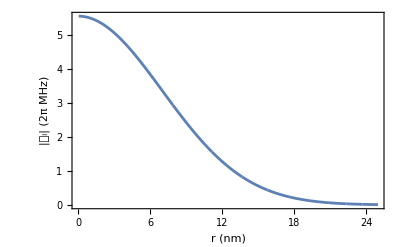

```mathematica
ListPlot[Transpose@{rcounts,Abs[avalscount]},PlotRange->All,Joined-> True, Frame-> True, FrameStyle->Directive[Black, 20], FrameLabel->{"r (nm)","|(|01d44e)_i| (2π MHz)"}]
```

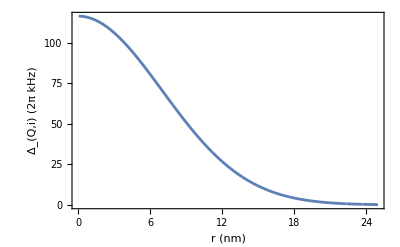

```mathematica
ListPlot[Transpose@{rcounts,qvalscount*1000},PlotRange->All,Joined-> True, Frame-> True, FrameStyle->Directive[Black, 20], FrameLabel->{"r (nm)","Δ_(Q,i) (2π kHz)"}]
```

### Fig. 2(c)

```mathematica
(* Using distributions given above, we can compute the nuclear one-tangling power *)
anc1 = 2π*0.0051;
ωn1 = 2π*12.98;
θ1 = π/3;

(* These matrices correspond to H0 and H1 that form rotation operators *)
M1[i_]:=ωn1 Iz+1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));
M2[i_]:=ωn1 Iz-1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));

M1Listtest = ParallelTable[M1[i],{i,Length[avalscount]}];
M2Listtest = ParallelTable[M2[i],{i,Length[avalscount]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t];
```

```mathematica
R0test = R0freetest[t];
R1test = R1freetest[t];
R0testdag = R0freetestdag[t];
R1testdag = R1freetestdag[t];

(* Computing G1 for each hyperfine coupling value associated with a given radial position *)
d = 4;
G1test[i_] := 1/d^2 Tr[R0test[[i]].R1testdag[[i]]]*Tr[R0testdag[[i]].R1test[[i]]];
G1testlist = Map[G1test,Range[Length[avalscount]]];
```

```mathematica
(* Computing nuclear one-tangling power at each position *)
epsilonnuc = 1/3(d/(d+1))(1 - G1testlist)/. t-> 5.32;


(* Computing analytical nuclear one-tangling power *)
```

```mathematica
G1freeanalytical[a_] := 1/2 Cos[a t]^2(1 + Cos[a t]);
G1freelist = ParallelTable[G1freeanalytical[avalscount[[i]]],{i,Length[avalscount]}];

epsilonanalytical = 1/3(d/(d+1))(1 - G1freelist)/. t-> 5.32;

ListPlot[{Transpose[{rcounts,epsilonanalytical}],Transpose[{rcounts,epsilonnuc}]},Joined->True,Frame->True,FrameLabel->{"r (nm)","\!\(\*SuperscriptBox[\(ϵ\), \(nuclear\)]\)"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20], PlotStyle->{Thick,Dashed}, PlotLegends-> Placed[{"Numerical","Analytical"}, {Center, Above}]]
```

-Graphics-

### Fig. 2(d)

```mathematica
(* Electronic one-tangling power for distribution of nuclear spins simulated above *)

(* Parameters in MHz where applicable *)
anc1 = 2π*0.0051;
ωn1 = 2π*12.98;

θ1 = π/3;

tstart = 0;
tend = 0.0078;
tstep =0.00011; 
tvals = ParallelTable[t,{t,tstart,tend,tstep}]//N; 

(* Calculate electronic one-tangling power for freely evolving electron coupled to 80000 nuclei *)

(* These matrices correspond to H0 and H1 that form rotation operators *)
M1[i_]:=ωn1 Iz+1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));
M2[i_]:=ωn1 Iz-1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));

M1Listtest = Table[M1[i],{i,Length[avalscount]}];
M2Listtest = Table[M2[i],{i,Length[avalscount]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t];

R0test = R0freetest[t];
R1test = R1freetest[t];
R0testdag = R0freetestdag[t];
R1testdag = R1freetestdag[t];

(* Computing G1 = |Tr[R0*R1^†]|^2 in two parts *)
G1freept1 = MapThread[#1.#2&, {R0test,R1testdag}];
G1freept2 = MapThread[#1.#2&, {R0testdag,R1test}];

(* Taking the trace of each part above before multiplying them together *)
TrG1freept1 = Map[Tr,G1freept1];
TrG1freept2 = Map[Tr,G1freept2];

d = 4;
(* Computing G1 *)
G1free = 1/d^2 TrG1freept1*TrG1freept2;

(* Multiplying together each G1 correponding to a given nuclear spin interacting with the electron *)

sepprod = Times @@ (1 + d G1free)/. t-> tvals;

(* Computing one-tangling power *)
epsilonfree = 1/3-1/3(1/(d+1))^Length[avalscount]*sepprod;
```

```mathematica
(* Computing the analytical free evolution electronic one-tangling power *)
G1freeanalytical[a_,t_] := 1/2 Cos[a t]^2(1 + Cos[a t]);

G1avals[t_]:= ParallelTable[G1freeanalytical[a,t],{a,avalscount}];

d = 4;
Prodsanalytical = {};
For[i=1,i<= Length[tvals],i++, AppendTo[Prodsanalytical, Fold[Times,1,(1+ d G1avals[tvals[[i]]])]]];

epeanalytical= 1/3-1/3(1/(d+1))^Length[avalscount]*Prodsanalytical;
```

```mathematica
(* Combining analytical and numerical results *)
ListPlot[{Transpose[{tvals*1000,epsilonfree}],Transpose[{tvals*1000,epeanalytical}]},Joined->True,Frame->True,FrameLabel->{"time (ns)","\!\(\*SuperscriptBox[\(ϵ\), \(electronic\)]\)"},LabelStyle->{"Black",20},FrameStyle->Directive[Black,20], PlotRange-> All, PlotStyle->{Thick, Dashed},PlotLegends-> Placed[{"Numerical","Analytical"}, {Center, Above}]]
```

-Graphics-

## Fig. 3

### Run this first: calculate distributions of hyperfine and quadrupolar coupling strengths

```mathematica
(* First solve for the density of spins per area in the dot *)
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.056;(* dr *)

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;

(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

θ1 = π/3;
qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2); 

(* For a given position r we have a hf coupling parameter corresponding to it. The number of nuclei located at this position r will dictate the number of times we include that given hf coupling value *)
avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius *)
rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten;
```

```mathematica
(* Number of nuclei is given by rcounts *)
rcounts//Length
```

### Fig. 3(a)(* Maybe check smaller step size *)

```mathematica
(* This plot is very memory and time intensive and needs to be run in chunks to get the rull range of values shown in the paper or run on a cluster. *)
```

```mathematica
anc1 = 2π*0.0051;
ωn1 = 2π*12.98;
θ1 = π/3;

tstart = 0.001;
tend = 1;
tstep = 0.071;
tvals = ParallelTable[t,{t,tstart, tend, tstep}];
epeCPMG = eop[tvals];
```

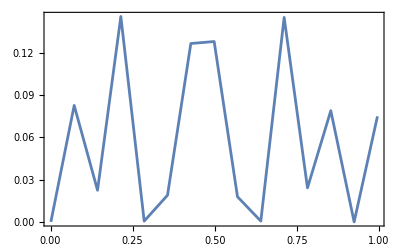

```mathematica
ListPlot[Transpose[{tvals,epeCPMG}], Frame-> True, Joined-> True]
```

```mathematica
(* Free evolution analytical *)
G1freeanalytical[a_,t_] := 1/2 Cos[a t]^2(1 + Cos[a t]);
G1avals[t_]:= ParallelTable[G1freeanalytical[a,t],{a,avalscount}]//Chop;

d = 4;
Prodsanalytical = {};
For[i=1,i<= Length[tvals],i++, AppendTo[Prodsanalytical, Fold[Times,1,(1+ d G1avals[tvals[[i]]])]]];

Prodsanalytical = Prodsanalytical//Chop;

epeanalytical= 1/3-1/3(1/(d+1))^Length[avalscount]*Prodsanalytical;
```

```mathematica
ListPlot[{Transpose[{tvals,epeanalytical}],Transpose[{tvals,epeCPMG}]},Joined->True, Frame->True,FrameLabel->{"time (μs)","ϵ^electronic"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20], PlotLegends->Placed[{"Free evolution","CPMG evolution"},{Center,Above}], ScalingFunctions->{"Log10", None}(* FrameTicks->{{Automatic, Automatic},{{10^-3,10^-2,10^-1,10^0,10^1,10^2,10^3}, Automatic}} *)]
```

-Graphics-

### Fig. 3(b) (* need to test larger step size *)

```mathematica
anc1 = 2π*0.58; θ1 = π/3;

(* original omega and time values used in paper--these take a very long time to generate the plot if not running on a cluster *)

(* ωstart = 2π*5.67; ωend = 13.2*2π; ωstep =0.096*2π;
ωvals = ParallelTable[ω, {ω, ωstart, ωend, ωstep}];

tstart = 0; tend = 0.1; tstep =0.00006; 
tvals = ParallelTable[t,{t,tstart,tend,tstep}]; *)

(* test for smaller step size *)
ωstart = 2π*5.67; ωend = 13.2*2π; ωstep =0.296*2π;
ωvals = ParallelTable[ω, {ω, ωstart, ωend, ωstep}];

tstart = 0; tend = 0.1; tstep =0.00006; 
tvals = ParallelTable[t,{t,tstart,tend,tstep}];
```

```mathematica
(* takes several hours to run with the parameters above-- consider smaller step size if speedup is desired. Also consider running on a cluster *)
eopdiffomega = Table[eopCPMGsmall[ω,tvals],{ω, ωvals}];
```

```mathematica
test = ResourceFunction["CombinePlots"];
test[ListPlot[Transpose[{ωvals/(2π),dephasingtimes*1000}] , Joined-> True, Frame-> True,FrameLabel->{"ω_i/2π (MHz)","time (ns)"},LabelStyle->{"Black",15},PlotRange->All,FrameStyle->Directive[Black,15]], ListPlot[Transpose[{ωvals/(2π),(Maxvals-1/3) *10^5}], Joined-> True, Frame-> True,PlotStyle->Red, FrameLabel->{"ω_i/2π (MHz)","(ϵ^electronic-1/3)×10^5"},LabelStyle->{"Black",15},PlotRange->All,FrameStyle->Directive[Red,15]], "AxesSides"-> "TwoY"]
```

## Fig. 4 (see Khadija’s code for 4(b))

### Figs. 4(a), (c), (d)

```mathematica
(* Parameters *)
ωn1 = 12.98*2π;
Dq1 = 2π*0.034;
anc1 = 2π*0.058;

(****  Change θ1 for each subfigure and the rest of the code is the same ****)
θ1 = π/4; 

(* Range of values for x and y axes--the code slows down pretty easily if there are too many values. I think it takes about 2.5 minutes for these parameters below (45 avals, 45 Dqvals, and 220 tvals). NOTE: always make sure avals and Dqvals have the same dimension. *)
astart =0;
aend = 2.5*ωn1;
astep = 0.0250*2π;
avals = Table[a,{a,astart,aend,astep}];

Dqstart = 0;
Dqend = 2.5*ωn1 ;
Dqstep =0.0250*2π ;
Dqvals = Table[Dq,{Dq,Dqstart,Dqend,Dqstep}];

t = 23.4;

(* Define H0, H1 matrices formed by plugging in all possible a and Dq values. 
These are the nuclear parts of the Hamiltonian given by H = Subscript[σ, 00]⊗Subscript[H, 0]+ Subscript[σ, 11]⊗Subscript[H, 1]  *)
M12[a_,Dq_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t/2;
M14[a_,Dq_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t/4;
M22[a_,Dq_]:=(ωn1 Iz -1/2 a Iz+Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t/2;
M24[a_,Dq_]:=(ωn1 Iz -1/2 a Iz+Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t/4;

(* Here we are just generating all possible values of Subscript[H, 0], Subscript[H, 1]. This method saves us time but costs a bit on memory. 
If you want something more memory-efficient I can give you another version. *)
M1List4 = ParallelTable[M14[i,j],{i,avals},{j,Dqvals}];
M2List4 = ParallelTable[M24[i,j],{i,avals},{j,Dqvals}];
M1List2 = ParallelTable[M12[i,j],{i,avals},{j,Dqvals}];
M2List2 = ParallelTable[M22[i,j],{i,avals},{j,Dqvals}];

(* Form free evolution rotations. These are the Subscript[R, i]= e^(-Subscript[iH, i]t) that we need to form the CPMG rotations. *)
R04=Map[MatrixExp[-I*#]&,M1List4,{2}];
R14=Map[MatrixExp[-I*#]&,M2List4,{2}];

R0dag4=Map[MatrixExp[I*#]&,M1List4,{2}];
R1dag4=Map[MatrixExp[I*#]&,M2List4,{2}];

R02=Map[MatrixExp[-I*#]&,M1List2,{2}];
R12=Map[MatrixExp[-I*#]&,M2List2,{2}];

R0dag2=Map[MatrixExp[I*#]&,M1List2,{2}];
R1dag2=Map[MatrixExp[I*#]&,M2List2,{2}];

(* Form CPMG evolution rotations. These are given by Subscript[R, i]^CPMG= Subscript[R, i](t/4)Subscript[R, j](t/2)Subscript[R, i](t/4) *)
R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},2];
R0CPMGdag = MapThread[#1.#2.#3&, {R0dag4,R1dag2,R0dag4},2];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},2];
R1CPMGdag = MapThread[#1.#2.#3&,{R1dag4, R0dag2, R1dag4},2];

(* Now we can compute Subscript[G, 1] = |Tr[(Subscript[R, 0]^CPMG)^†Subscript[R, 1]^CPMG]|^2. We do this in three parts: First we multiply (Subscript[R, 0]^CPMG)^† with Subscript[R, 1]^CPMG and multiply Subscript[R, 0]^CPMG with (Subscript[R, 1]^CPMG)^†.  *)
G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},2];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},2];
(* Then we take the trace of each *)
TrG1CPMGpt1 = Map[Tr,G1CPMGpt1, {2}];
TrG1CPMGpt2 = Map[Tr,G1CPMGpt2, {2}];
(* Then we multiply them together, with the appropriate normalization of 1/d^2 where d is the dimension of the nuclear spin we're interested in. *)
d = Length[Iz];

G1CPMG = 1/d^2 TrG1CPMGpt1*TrG1CPMGpt2;

(* We can use the CPMG Subscript[G, 1] to compute the nuclear one-tangling power: *)
ep = 1/3(d/(d+1))(1 - G1CPMG);

(* This just collects all the sets of data we need for the density plot *)xyzPairs = Table[Transpose@{avals[[j]]/ωn1,Dqvals[[k]]/ωn1,ep[[j]][[k]]},{j,1,Length[avals]},{k,1,Length[Dqvals]}];
xyzPairs = Flatten[xyzPairs,1];
xyzPairs = xyzPairs//Chop;

ListDensityPlot[xyzPairs, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"(|(|01d44e)_1|)/ω_1","(Δ_(Q, 1))/ω_1"},LabelStyle-> {Directive[ Black],25}]
```

### Figs. 4(e), (f)

```mathematica
anc1 = 2π*0.051;
θ1 = π/3;

ωn1 = 1/2 Abs[Mean[avalscount]]; (**** Change the value of ωn1 to 2π*12.98; for 4(e) ****)
Dq1 = 2π*0.34;

tstart = 0;
tend = 23.4;
tstep = 0.11; 
tvals = Table[t,{t,tstart,tend,tstep}]//N;

(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[i_,t_]:=(ωn1 Iz+1/2 avalscount[[i]] Iz+Dq1 Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[i_,t_]:=(ωn1 Iz-1/2 avalscount[[i]] Iz+Dq1 Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t; 

M1List4 = ParallelTable[M1[i,t/4],{i,Length[rcounts]},{t,tvals}];
M2List4 = ParallelTable[M2[i,t/4],{i,Length[rcounts]},{t,tvals}];

M1List2 = ParallelTable[M1[i,t/2],{i,Length[rcounts]},{t,tvals}];
M2List2 = ParallelTable[M2[i,t/2],{i,Length[rcounts]},{t,tvals}];

(* Form free evolution rotation operators for each part of the CPMG sequence *)
R04=Map[MatrixExp[-I*#]&,M1List4,{2}];
R14=Map[MatrixExp[-I*#]&,M2List4,{2}];

R04dag=Map[MatrixExp[I*#]&,M1List4,{2}];
R14dag=Map[MatrixExp[I*#]&,M2List4,{2}];

R02=Map[MatrixExp[-I*#]&,M1List2,{2}];
R12=Map[MatrixExp[-I*#]&,M2List2,{2}];

R02dag=Map[MatrixExp[I*#]&,M1List2,{2}];
R12dag=Map[MatrixExp[I*#]&,M2List2,{2}];

(* Combine free evolution rotation operators to form CPMG rotation for a single iteration of the sequence *)
R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},2];
R0CPMGdag = MapThread[#1.#2.#3&, {R04dag,R12dag,R04dag},2];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},2];
R1CPMGdag = MapThread[#1.#2.#3&,{R14dag, R02dag, R14dag},2];

(* Compute G1 in two parts *)
G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},2];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},2];

(*Compute traces for each element in G1pt1 and G1pt2*)
TrG1CPMGpt1=Map[Tr,G1CPMGpt1,{2}];
TrG1CPMGpt2=Map[Tr,G1CPMGpt2,{2}];

(*Compute the product of the traces*)
G1CPMG=1/16 TrG1CPMGpt1*TrG1CPMGpt2;

(* Compute one-tangling power *)
epCPMG = 4/15(1 - G1CPMG);

xyzPairsCPMG = Table[Transpose@{rcounts[[j]],tvals[[k]],epCPMG[[j]][[k]]},{j,1,Length[rcounts]},{k,1,Length[tvals]}];

xyzPairsCPMG = Flatten[xyzPairsCPMG,1];
```

```mathematica
ListDensityPlot[xyzPairsCPMG, PlotLegends-> Automatic,PlotRange-> All, Frame->True,FrameLabel->{"r (nm)","t (μs)"},LabelStyle-> {Directive[ Black],20}, MaxPlotPoints->200]
```

-Graphics-

### Fig. 4(g)

```mathematica
(* Similar to above, but now plugging in values from quadrupolar coupling distribution as well as hyperfine *)
```

```mathematica
anc1 = 2π*0.051;
θ1 = π/3;

ωn1 = 1/2 Abs[Mean[avalscount]];
Dq1 = 2π*0.34;

tstart = 0;
tend = 23.4;
tstep = 0.11; 
tvals = Table[t,{t,tstart,tend,tstep}]//N;

(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[i_,t_]:=(ωn1 Iz+1/2 avalscount[[i]] Iz+qvalscount[[i]] Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[i_,t_]:=(ωn1 Iz-1/2 avalscount[[i]] Iz+ qvalscount[[i]] Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t; 

M1List4 = ParallelTable[M1[i,t/4],{i,Length[rcounts]},{t,tvals}];
M2List4 = ParallelTable[M2[i,t/4],{i,Length[rcounts]},{t,tvals}];

M1List2 = ParallelTable[M1[i,t/2],{i,Length[rcounts]},{t,tvals}];
M2List2 = ParallelTable[M2[i,t/2],{i,Length[rcounts]},{t,tvals}];

(* Form free evolution rotation *)
R04=Map[MatrixExp[-I*#]&,M1List4,{2}];
R14=Map[MatrixExp[-I*#]&,M2List4,{2}];

R04dag=Map[MatrixExp[I*#]&,M1List4,{2}];
R14dag=Map[MatrixExp[I*#]&,M2List4,{2}];

R02=Map[MatrixExp[-I*#]&,M1List2,{2}];
R12=Map[MatrixExp[-I*#]&,M2List2,{2}];

R02dag=Map[MatrixExp[I*#]&,M1List2,{2}];
R12dag=Map[MatrixExp[I*#]&,M2List2,{2}];

(* CPMG rotation operators *)
R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},2];
R0CPMGdag = MapThread[#1.#2.#3&, {R04dag,R12dag,R04dag},2];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},2];
R1CPMGdag = MapThread[#1.#2.#3&,{R14dag, R02dag, R14dag},2];

G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},2];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},2];

(*Compute traces for each element in G1pt1 and G1pt2*)
TrG1CPMGpt1=Map[Tr,G1CPMGpt1,{2}];
TrG1CPMGpt2=Map[Tr,G1CPMGpt2,{2}];

(*Compute the product of the traces*)
G1CPMG=1/16 TrG1CPMGpt1*TrG1CPMGpt2;

(* Compute nuclear one-tangling power *)
epCPMG = 4/15(1 - G1CPMG);

xyzPairsCPMG = Table[Transpose@{rcounts[[j]],tvals[[k]],epCPMG[[j]][[k]]},{j,1,Length[rcounts]},{k,1,Length[tvals]}];

xyzPairsCPMG = Flatten[xyzPairsCPMG,1];
```

## Fig. 5

### Fig. 5(a)

```mathematica
a1 = 0.23 *2π;
Dq1 =2π*0.0058;

anc1 = 2π*0.021;
θ1 = π/3;

ωvals = Table[ω,{ω, 0,5, 0.026}];

tstart = 0;
tend = 45.6;
tstep = 0.041; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 

(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[ωn1_,t_]:=(ωn1 Iz+1/2 a1 Iz+Dq1 Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[ωn1_,t_]:=(ωn1 Iz-1/2 a1 Iz+Dq1 Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t; 

M1List = ParallelTable[M1[i,t],{i,ωvals},{t,tvals}];
M2List = ParallelTable[M2[i,t],{i,ωvals},{t,tvals}];

(* Form free evolution rotation *)
R0=Map[MatrixExp[-I*#]&,M1List,{2}];
R1=Map[MatrixExp[-I*#]&,M2List,{2}];

R0dag=Map[MatrixExp[I*#]&,M1List,{2}];
R1dag=Map[MatrixExp[I*#]&,M2List,{2}];

G1pt1 = MapThread[Dot[#1,#2]&,{R0,R1dag},2];
G1pt2 = MapThread[Dot[#1,#2]&,{R0dag,R1},2];

(*Compute traces for each element in G1pt1 and G1pt2*)
TrG1pt1=Map[Tr,G1pt1,{2}];
TrG1pt2=Map[Tr,G1pt2,{2}];

(*Compute the product of the traces*)
G1=1/16 TrG1pt1*TrG1pt2;

(* Compute one-tangling power *)
ep = 4/15(1 - G1);

xyzPairs = Table[Transpose@{ωvals[[j]],tvals[[k]],ep[[j]][[k]]},{j,1,Length[ωvals]},{k,1,Length[tvals]}];
xyzPairs = Flatten[xyzPairs,1];

ListDensityPlot[xyzPairs, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"ω_1 (MHz)","t (μs)"},LabelStyle-> {Directive[ Black],20},MaxPlotPoints->200]
```

-Graphics-

### Fig. 5(b)

```mathematica
a1 = 0.23 *2π;
ωn1 =1/2 a1;

anc1 = 2π*0.021;
θ1 = π/3;

Dqvals = Table[ω,{ω, 0,5, 0.026}];

tstart = 0;
tend = 45.6;
tstep = 0.041; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 


(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[Dq1_,t_]:=(ωn1 Iz+1/2 a1 Iz+Dq1 Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[Dq1_,t_]:=(ωn1 Iz-1/2 a1 Iz+Dq1 Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t; 

M1List = ParallelTable[M1[i,t],{i,Dqvals},{t,tvals}];
M2List = ParallelTable[M2[i,t],{i,Dqvals},{t,tvals}];
(* Form free evolution rotation *)
R0=Map[MatrixExp[-I*#]&,M1List,{2}];
R1=Map[MatrixExp[-I*#]&,M2List,{2}];

R0dag=Map[MatrixExp[I*#]&,M1List,{2}];
R1dag=Map[MatrixExp[I*#]&,M2List,{2}];

G1pt1 = MapThread[Dot[#1,#2]&,{R0,R1dag},2];
G1pt2 = MapThread[Dot[#1,#2]&,{R0dag,R1},2];

(*Compute traces for each element in G1pt1 and G1pt2*)
TrG1pt1=Map[Tr,G1pt1,{2}];
TrG1pt2=Map[Tr,G1pt2,{2}];

(*Compute the product of the traces*)
G1=1/16 TrG1pt1*TrG1pt2;

(* Compute one-tangling power *)
ep = 4/15(1 - G1);

xyzPairs = Table[Transpose@{Dqvals[[j]],tvals[[k]],ep[[j]][[k]]},{j,1,Length[Dqvals]},{k,1,Length[tvals]}];

xyzPairs = Flatten[xyzPairs,1];

ListDensityPlot[xyzPairs, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"Δ_(Q, 1) (MHz)","t (μs)"},LabelStyle-> {Directive[ Black],20}, MaxPlotPoints->200]
```

### Fig. 5(c)

```mathematica
a1 = 0.23 *2π;
Dq1 =2π*0.0058;

anc1 = 2π*0.021;
θ1 = π/3;

ωvals = Table[ω,{ω, 0,5, 0.026}];

tstart = 0;
tend = 45.6;
tstep = 0.041; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 

(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[ωn1_,t_]:=(ωn1 Iz+1/2 a1 Iz+Dq1 Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[ωn1_,t_]:=(ωn1 Iz-1/2 a1 Iz+Dq1 Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t; 

M1List4 = ParallelTable[M1[i,t/4],{i,ωvals},{t,tvals}];
M2List4 = ParallelTable[M2[i,t/4],{i,ωvals},{t,tvals}];

M1List2 = ParallelTable[M1[i,t/2],{i,ωvals},{t,tvals}];
M2List2 = ParallelTable[M2[i,t/2],{i,ωvals},{t,tvals}];

(* Form free evolution rotation *)
R04=Map[MatrixExp[-I*#]&,M1List4,{2}];
R14=Map[MatrixExp[-I*#]&,M2List4,{2}];

R04dag=Map[MatrixExp[I*#]&,M1List4,{2}];
R14dag=Map[MatrixExp[I*#]&,M2List4,{2}];

R02=Map[MatrixExp[-I*#]&,M1List2,{2}];
R12=Map[MatrixExp[-I*#]&,M2List2,{2}];

R02dag=Map[MatrixExp[I*#]&,M1List2,{2}];
R12dag=Map[MatrixExp[I*#]&,M2List2,{2}];

R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},2];
R0CPMGdag = MapThread[#1.#2.#3&, {R04dag,R12dag,R04dag},2];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},2];
R1CPMGdag = MapThread[#1.#2.#3&,{R14dag, R02dag, R14dag},2];

G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},2];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},2];

(*Compute traces for each element in G1pt1 and G1pt2*)
TrG1CPMGpt1=Map[Tr,G1CPMGpt1,{2}];
TrG1CPMGpt2=Map[Tr,G1CPMGpt2,{2}];

(*Compute the product of the traces*)
G1CPMG=1/16 TrG1CPMGpt1*TrG1CPMGpt2;

(* Compute one-tangling power *)
epCPMG = 4/15(1 - G1CPMG);

xyzPairsCPMG = Table[Transpose@{ωvals[[j]],tvals[[k]],epCPMG[[j]][[k]]},{j,1,Length[ωvals]},{k,1,Length[tvals]}];
xyzPairsCPMG = Flatten[xyzPairsCPMG,1];
```

```mathematica
ListDensityPlot[xyzPairsCPMG, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"ω_1 (MHz)","t (μs)"},LabelStyle-> {Directive[ Black],20}, MaxPlotPoints->200, GridLines->{{a1/2},{}}, GridLinesStyle->Directive[Gray, Thick]]
```

-Graphics-

### Fig. 5(d)

```mathematica
a1 = 0.23 *2π;
ωn1 =1/2 a1;

anc1 = 2π*0.021;
θ1 = π/3;

Dqvals = Table[ω,{ω, 0,5, 0.026}];

tstart = 0;
tend = 45.6;
tstep = 0.041; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 


(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[Dq1_,t_]:=(ωn1 Iz+1/2 a1 Iz+Dq1 Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[Dq1_,t_]:=(ωn1 Iz-1/2 a1 Iz+Dq1 Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t; 

M1List4 = ParallelTable[M1[i,t/4],{i,Dqvals},{t,tvals}];
M2List4 = ParallelTable[M2[i,t/4],{i,Dqvals},{t,tvals}];

M1List2 = ParallelTable[M1[i,t/2],{i,Dqvals},{t,tvals}];
M2List2 = ParallelTable[M2[i,t/2],{i,Dqvals},{t,tvals}];

(* Form free evolution rotation *)
R04=Map[MatrixExp[-I*#]&,M1List4,{2}];
R14=Map[MatrixExp[-I*#]&,M2List4,{2}];

R04dag=Map[MatrixExp[I*#]&,M1List4,{2}];
R14dag=Map[MatrixExp[I*#]&,M2List4,{2}];

R02=Map[MatrixExp[-I*#]&,M1List2,{2}];
R12=Map[MatrixExp[-I*#]&,M2List2,{2}];

R02dag=Map[MatrixExp[I*#]&,M1List2,{2}];
R12dag=Map[MatrixExp[I*#]&,M2List2,{2}];


R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},2];
R0CPMGdag = MapThread[#1.#2.#3&, {R04dag,R12dag,R04dag},2];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},2];
R1CPMGdag = MapThread[#1.#2.#3&,{R14dag, R02dag, R14dag},2];

G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},2];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},2];

(*Compute traces for each element in G1pt1 and G1pt2*)
TrG1CPMGpt1=Map[Tr,G1CPMGpt1,{2}];
TrG1CPMGpt2=Map[Tr,G1CPMGpt2,{2}];

(*Compute the product of the traces*)
G1CPMG=1/16 TrG1CPMGpt1*TrG1CPMGpt2;

(* Compute one-tangling power *)
epCPMG = 4/15(1 - G1CPMG);

xyzPairsCPMG = Table[Transpose@{Dqvals[[j]],tvals[[k]],epCPMG[[j]][[k]]},{j,1,Length[Dqvals]},{k,1,Length[tvals]}];
xyzPairsCPMG = Flatten[xyzPairsCPMG,1];
```

```mathematica
ListDensityPlot[xyzPairsCPMG, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"Δ_(Q, 1) (MHz)","t (μs)"},LabelStyle-> {Directive[ Black],20}, MaxPlotPoints->200,  GridLines->{{0, a1/2, a1},{}}, GridLinesStyle->Directive[Gray, Thick]]
```

## Fig. 6

### Run first: generates distributions for hyperfine and quadrupolar parameters

```mathematica
(* Creating smaller distributions *)
(* First solve for the density of spins per area in the dot *)
NN = 200;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.056;(* dr *)

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;

(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

θ1 = π/3;
qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);
avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius *)
rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten;
```

### Figs. 6(a), (b), (c)

```mathematica
(* t in us *)
tstart = 0; 
tend = 17.6;
tstep = 0.01;
tvals = ParallelTable[t, {t, tstart, tend, tstep}];
```

```mathematica
a1 = 0.23*2π;
ωn1 = 12.98*2π;
Dq1 = 2π*0.034;
anc1 = 2π*0.056;
θ1 = π/3;
NN = 1;
nucCPMGvals = nuclearonetangleCPMG[ωn1, a1, Dq1, anc1, θ1,NN, tvals];
(**** For 6(b), just change a^nc value above to anc1 = 2π*2.3; ****)
(**** For 6(c), just change NN value above to NN = 85; ****)
```

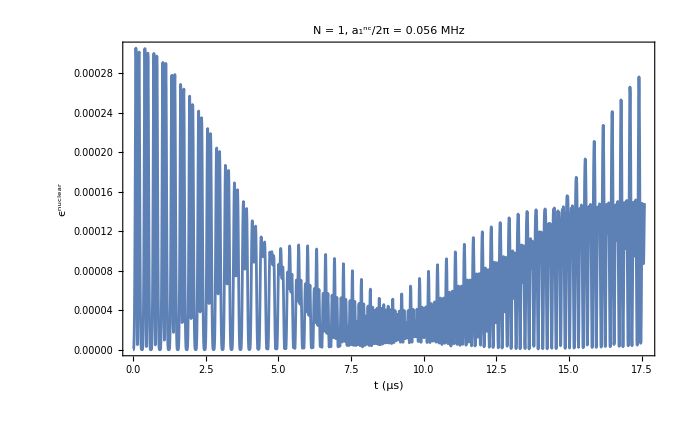

```mathematica
(* Fig. 1(a): Free evolution nuclear one-tangling power *)
ListPlot[Transpose[{tvals,nucCPMGvals}], Frame-> True,Joined-> True,FrameLabel->{"t (μs)","ϵ^nuclear"}, LabelStyle->{Directive[Black],30}, FrameStyle->Directive[Black], PlotLabel-> "N = 1, a_1^nc/2π = 0.056 MHz"]
```

### Figs. 6(d), (e)

```mathematica
(***** Note: for the plots in the paper a smaller step size is used in the generation of avals and Dqvals below. This is memory and time-intensive so I broke this code into chunks and pieced them together. Alternatively I recommend running this on a cluster if smoother plots are desired. *****)
```

```mathematica
(* Parameters *)
ωn1 = 12.98*2π;
anc1 = 2π*0.063; (**** For 6(e) change to 2π*1.3 ****)
θ1 = π/3;

(* Range of values for x and y axes--the code slows down pretty easily if there are too many values. I think it takes about 2.5 minutes for these parameters below (45 avals, 45 Dqvals, and 220 tvals) *)
astart =0;
aend = 2.5*ωn1;
astep = 0.50*2π;
avals = Table[a,{a,astart,aend,astep}];

Dqstart = 0;
Dqend = 2.5*ωn1 ;
Dqstep =0.50*2π ;
Dqvals = Table[Dq,{Dq,Dqstart,Dqend,Dqstep}];

tstart = 0;
tend = 36.7;
tstep = 0.071; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 

(* Define H0, H1 matrices formed by plugging in all possible a and Dq values. 
These are the nuclear parts of the Hamiltonian given by H = Subscript[σ, 00]⊗Subscript[H, 0]+ Subscript[σ, 11]⊗Subscript[H, 1]  *)
M1[a_,Dq_,t_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[a_,Dq_,t_]:=(ωn1 Iz -1/2 a Iz+Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t;

(* Here we are just generating all possible values of Subscript[H, 0], Subscript[H, 1]. This method saves us time but costs a bit on memory. 
If you want something more memory-efficient I can give you another version. *)
M1List4 = ParallelTable[M1[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M2List4 = ParallelTable[M2[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M1List2 = ParallelTable[M1[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];
M2List2 = ParallelTable[M2[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];

(* Form free evolution rotations. These are the Subscript[R, i]= e^(-Subscript[iH, i]t) that we need to form the CPMG rotations. *)
R04=Map[MatrixExp[-I*#]&,M1List4,{3}];
R14=Map[MatrixExp[-I*#]&,M2List4,{3}];

R0dag4=Map[MatrixExp[I*#]&,M1List4,{3}];
R1dag4=Map[MatrixExp[I*#]&,M2List4,{3}];

R02=Map[MatrixExp[-I*#]&,M1List2,{3}];
R12=Map[MatrixExp[-I*#]&,M2List2,{3}];

R0dag2=Map[MatrixExp[I*#]&,M1List2,{3}];
R1dag2=Map[MatrixExp[I*#]&,M2List2,{3}];

(* Form CPMG evolution rotations. These are given by Subscript[R, i]^CPMG= Subscript[R, i](t/4)Subscript[R, j](t/2)Subscript[R, i](t/4) *)
R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},3];
R0CPMGdag = MapThread[#1.#2.#3&, {R0dag4,R1dag2,R0dag4},3];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},3];
R1CPMGdag = MapThread[#1.#2.#3&,{R1dag4, R0dag2, R1dag4},3];

(* Now we can compute Subscript[G, 1] = |Tr[(Subscript[R, 0]^CPMG)^†Subscript[R, 1]^CPMG]|^2. We do this in three parts: First we multiply (Subscript[R, 0]^CPMG)^† with Subscript[R, 1]^CPMG and multiply Subscript[R, 0]^CPMG with (Subscript[R, 1]^CPMG)^†.  *)
G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},3];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},3];
(* Then we take the trace of each *)
TrG1CPMGpt1 = Map[Tr,G1CPMGpt1, {3}];
TrG1CPMGpt2 = Map[Tr,G1CPMGpt2, {3}];
(* Then we multiply them together, with the appropriate normalization of 1/d^2 where d is the dimension of the nuclear spin we're interested in. *)
d = Length[Iz];
G1CPMG = 1/d^2 TrG1CPMGpt1*TrG1CPMGpt2;

(* We can use the CPMG Subscript[G, 1] to compute the nuclear one-tangling power: *)
ep = 1/3(d/(d+1))(1 - G1CPMG);

(* To create a time-optimized plot, we now take the max of the one-tangling power for each pair of values in avals and Dqvals. This grabs the maximal value of the one-tangling power that we can have for those parameters over the time interval we're checking.  *)
maxvals=Apply[Max,ep,{2}];

(* This just collects all the sets of data we need for the density plot *)xyzPairs = Table[Transpose@{avals[[j]]/ωn1,Dqvals[[k]]/ωn1,maxvals[[j]][[k]]},{j,1,Length[avals]},{k,1,Length[Dqvals]}];
xyzPairs = Flatten[xyzPairs,1];
```

### Figs. 6(f), (g)

```mathematica
NN= 5; (**** Change to NN = 85 for 6(g) ****)

ωn1 = 12.98*2π;
anc1 = 2π*0.063 ;
θ1 = π/3;

(* Note: avals and Dqvals must be equal in dimension. Also, Increase the astep and Dqstep to make code run faster *)
astart = 0;
aend =ωn1;
astep = 0.250*2π;
avals = Table[a,{a,astart,aend,astep}];

Dqstart = 0;
Dqend = ωn1;
Dqstep =0.250*2π ; 
Dqvals = Table[Dq,{Dq,Dqstart,Dqend,Dqstep}];

tstart = 0;
tend = 36.7;
tstep = 0.071; (* increase this to make code run faster *)
tvals = Table[t,{t,tstart,tend,tstep}]//N; 

(* Time-optimized plots:N=5 CPMG *)
(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[a_,Dq_,t_]:=(ωn1 Iz+1/2 a Iz+Dq Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[a_,Dq_,t_]:=(ωn1 Iz-1/2 a Iz+Dq Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t;

M1List4 = ParallelTable[M1[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M2List4 = ParallelTable[M2[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M1List2 = ParallelTable[M1[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];
M2List2 = ParallelTable[M2[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];

(* Form free evolution rotation operators *)
R04=Map[MatrixExp[-I*#]&,M1List4,{3}];
R14=Map[MatrixExp[-I*#]&,M2List4,{3}];

R0dag4=Map[MatrixExp[I*#]&,M1List4,{3}];
R1dag4=Map[MatrixExp[I*#]&,M2List4,{3}];

R02=Map[MatrixExp[-I*#]&,M1List2,{3}];
R12=Map[MatrixExp[-I*#]&,M2List2,{3}];

R0dag2=Map[MatrixExp[I*#]&,M1List2,{3}];
R1dag2=Map[MatrixExp[I*#]&,M2List2,{3}];

(* Combine free evolution rotation operators over correct time intervals for CPMG sequence. NN corresponds to number of iterations of the CPMG sequence. *)
R0CPMG2 = MapThread[MatrixPower[#1.#2.#3,NN]&,{R04,R12,R04},3]//Chop;
R0CPMGdag2 = MapThread[MatrixPower[#1.#2.#3,NN]&, {R0dag4,R1dag2,R0dag4},3]//Chop;
R1CPMG2 = MapThread[MatrixPower[#1.#2.#3,NN]&, {R14,R02,R14},3]//Chop;
R1CPMGdag2 = MapThread[MatrixPower[#1.#2.#3,NN]&,{R1dag4, R0dag2, R1dag4},3]//Chop; 

(* Calculation of G1 *)
G1CPMGpt12 = MapThread[#1.#2&,{R0CPMG2,R1CPMGdag2},3];
G1CPMGpt22 = MapThread[#1.#2&,{R0CPMGdag2,R1CPMG2},3];

TrG1CPMGpt12 = Map[Tr,G1CPMGpt12, {3}];
TrG1CPMGpt22 = Map[Tr,G1CPMGpt22, {3}];

G1CPMG2 = 1/16 TrG1CPMGpt12*TrG1CPMGpt22;

(* Compute nuclear one-tangling power *)
ep2 = 4/15(1 - G1CPMG2)//Chop;

maxvals=Apply[Max,ep2,{2}];

xyzPairs = Table[Transpose@{avals[[j]]/ωn1,Dqvals[[k]]/ωn1,maxvals[[j]][[k]]},{j,1,Length[avals]},{k,1,Length[Dqvals]}];

xyzPairs = Flatten[xyzPairs,1];
ListDensityPlot[xyzPairs, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"a/ω_n","Δ/ω_n"},PlotLabel-> "Time-optimized ϵ^CPMG N=8",LabelStyle-> {Directive[ Black],20}]
```

## Figs. 7, 8 are given in another file and see Khadija’s code for 8(e)

## Fig. 9(c)

```mathematica
ωn1 = 12.98*2π;
anc1 = 2π*0.058 ;
θ1 = π/4;

astart =-4*ωn1;
aend = 4*ωn1;
astep = 0.750*2π;
avals = Table[a,{a,astart,aend,astep}];

Dqstart = -4*ωn1;
Dqend = 4*ωn1 ;
Dqstep =0.750*2π ;
Dqvals = Table[Dq,{Dq,Dqstart,Dqend,Dqstep}];

tstart = 0;
tend = 15.6;
tstep = 0.071; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 

(* Form H0, H1 for simpler non-collinear term *)
M1[a_,Dq_,t_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -1/2 (anc1 Ix ))t;
M2[a_,Dq_,t_]:=(ωn1 Iz -1/2 a Iz+Dq Iz.Iz +1/2 (anc1 Ix )) t;

(* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1List4 = ParallelTable[M1[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M2List4 = ParallelTable[M2[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M1List2 = ParallelTable[M1[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];
M2List2 = ParallelTable[M2[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];

(* Form free evolution rotation operators *)
R04=Map[MatrixExp[-I*#]&,M1List4,{3}];
R14=Map[MatrixExp[-I*#]&,M2List4,{3}];

R0dag4=Map[MatrixExp[I*#]&,M1List4,{3}];
R1dag4=Map[MatrixExp[I*#]&,M2List4,{3}];

R02=Map[MatrixExp[-I*#]&,M1List2,{3}];
R12=Map[MatrixExp[-I*#]&,M2List2,{3}];

R0dag2=Map[MatrixExp[I*#]&,M1List2,{3}];
R1dag2=Map[MatrixExp[I*#]&,M2List2,{3}];

(* CPMG rotation operators *)
R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},3];
R0CPMGdag = MapThread[#1.#2.#3&, {R0dag4,R1dag2,R0dag4},3];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},3];
R1CPMGdag = MapThread[#1.#2.#3&,{R1dag4, R0dag2, R1dag4},3];

(* Computing G1 *)
G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},3];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},3];

TrG1CPMGpt1 = Map[Tr,G1CPMGpt1, {3}];
TrG1CPMGpt2 = Map[Tr,G1CPMGpt2, {3}];

G1CPMG = 1/16 TrG1CPMGpt1*TrG1CPMGpt2;

(* Computing nuclear one-tangling power *)
ep = 4/15(1 - G1CPMG);

maxvals=Apply[Max,ep,{2}];

xyzPairs = Table[Transpose@{avals[[j]]/ωn1,Dqvals[[k]]/ωn1,maxvals[[j]][[k]]},{j,1,Length[avals]},{k,1,Length[Dqvals]}];

xyzPairs = Flatten[xyzPairs,1];
```

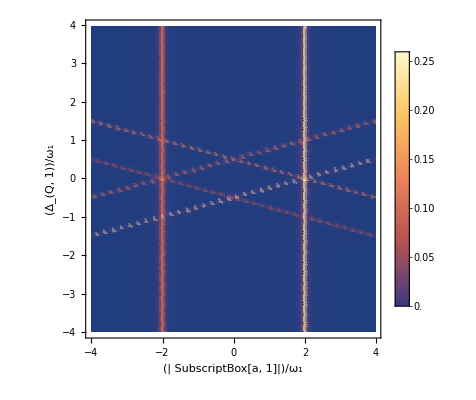

```mathematica
ListDensityPlot[xyzPairs, PlotLegends-> True,PlotRange-> All, Frame->True,FrameLabel->{"(| SubscriptBox[a, 1]|)/ω_1","(Δ_(Q, 1))/ω_1"}, LabelStyle-> {Directive[ Black],20}]
```